```mathematica
c[n_,m_]:=Binomial[n,m];
comb[N_,k_]:=Subsets[Table[i,{i,1,N}],{k}];
Num[x_]:=N[x];

HgMap[N_,k_]:=Module[{tab,ind1,listi,tabx,sites,flipsites,set1,flip,listf,xb,xa},
tab={};tabx={};
listi=comb[N,k];
sites=Table[i,{i,1,N}];
Do[
set1=listi[[i]];
flipsites=Complement[sites,set1];
Do[
flip=flipsites[[j]];
listf=Sort[Join[set1,{flip}]];
xa=c[N,k+1]-Sum[c[N-listf[[p+1]],k+1-p],{p,0,k}];
AppendTo[tabx,xa];
,{j,1,Length[flipsites]}];
AppendTo[tab,tabx];tabx={};
,{i,1,Length[listi]}];
tab] ;

mkHg[N_,m_,gg_]:=Module[
{pntr,ind1,ind2,coora,ntot,Hg,ind2sub,m1},

(* seperate case with saturated polarisation *)
m1=Min[m,N];(*If[m≤ N,m1=m,m1=N];*)
(* pointers for start index *)
pntr=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
ntot=pntr[[-1]];
Hg=SparseArray[{},{ntot,ntot}];
Do[
ind1=pntr[[k+1]]+Table[i,{i,1,c[N,k]}];
ind2=pntr[[k+2]]+HgMap[N,k];
(*Print[HgMap[N,k]];*)
coora={};
Do[ind2sub=ind2[[j]];
Do[AppendTo[coora, {ind1[[j]],ind2sub[[j2]]}];
,{j2,1,Length[ind2sub]}];
,{j,1,Length[ind1]}];
(* caution: Sqrt[m-k]*gg contains m, not m1 *)
Hg+=SparseArray[coora-> Sqrt[m-k]*gg,{ntot,ntot}];
,{k,0,m1-1}];
Hg//Num
];

DiagH[N_,m_,gg_]:=Module[{Hg,eval,U,Uct},
If[m>0,
Hg=mkHg[N,m,gg];Hg+=Transpose[Hg];
(* Sort, ascending order:
ref: https://stackoverflow.com/questions/6589005/sort-eigenvalue-matrix-with-eigenvector-matrix *)
{eval,U}=Transpose@SortBy[Transpose[Eigensystem[Hg]],First];
,
(* make E&U by hand *)
eval={0.0};U={{1.0}};
];
{eval,U//Transpose}
];

HgMapflip[N_,k_]:=Module[{tab,ind1,listi,tabx,sites,flipsites,set1,flip,listf,xb,xa,tabflip,tabflipx},
tab={};tabx={};tabflip={};tabflipx={};
listi=comb[N,k];
sites=Table[i,{i,1,N}];
Do[
set1=listi[[i]];
flipsites=Complement[sites,set1];
Do[
flip=flipsites[[j]];
listf=Sort[Join[set1,{flip}]];
xa=c[N,k+1]-Sum[c[N-listf[[p+1]],k+1-p],{p,0,k}];
AppendTo[tabx,xa];
AppendTo[tabflipx,flip];
,{j,1,Length[flipsites]}];
AppendTo[tab,tabx];tabx={};
AppendTo[tabflip,tabflipx];tabflipx={};
,{i,1,Length[listi]}];
{tab,tabflip}] ;


mkXb[ii_,NN_,M_]:=Module[{list,IM,xb},
xb=SparseArray[Table[{i,i+1}-> Sqrt[i],{i,1,M-1}],{M,M}];
xb += Transpose[xb];
(*xb//MatrixForm//Print;*)
list={};
IM=SparseArray[{Band[{1,1}]->1},{M,M}];
Do[
If[j==ii,AppendTo[list,xb],AppendTo[list,IM]]
,{j,1,NN}];
KroneckerProduct@@list
];

diagF=SparseArray[Band[{1,1}]->{##}]&;

(* makeHb[N=sites,M=vib_levels,m=exciton+photons], out = Hb in Full Hilnert space *)
makeHb[N_,M_,m_]:=Module[
{pntr,ind1,ind2,coora,ntot,Hg,ind2sub,m1,tab,tabflip,flips,i1,i2,iup,XB,Xb,Hb},
(* 1. make displacement operators Xb[i] = Subscript[b, i]+Subscript[b, i]^†*)
Do[Xb[i]=mkXb[i,N,M],{i,1,N}];
(* 2. make XB's for all basis states of electron-photon subsystem *)
(* starting state needs to be defined for all spin down: a zero matrix *)
XB[1]=SparseArray[{},{M^N,M^N}];
(* seperate case with saturated polarisation *)
m1=Min[m,N];(*If[m≤ N,m1=m,m1=N];*)
(* pointers for start index *)
pntr=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
ntot=pntr[[-1]];
Do[
ind1=pntr[[k+1]]+Table[i,{i,1,c[N,k]}];
{tab,tabflip}=HgMapflip[N,k];
ind2=pntr[[k+2]]+tab;
Do[
ind2sub=ind2[[j]];
flips=tabflip[[j]];
Do[
{i1,i2,iup}={ind1[[j]],ind2sub[[j2]],flips[[j2]]};
(* make the new Sum[Xb's] from old by adding the flip site's Xb *)
XB[i2]=XB[i1] + Xb[iup];
,{j2,1,Length[ind2sub]}];
,{j,1,Length[ind1]}];
,{k,0,m1-1}];

(* 3. place the XB's to the correct position in full Hilbert space *)
(* blocks of dim M^N corresponding to each elec-photon basis along its diagonal*)
Hb=diagF @@ Table[XB[i],{i,1,ntot}];
Hb+=Transpose[Hb];
Hb
];

makeHg[N_,M_,m_,gg_]:=Module[{Hg,Ivib,IM},
(*vib Identity *)
IM=SparseArray[{Band[{1,1}]->1},{M^N,M^N}];
(* Hg in elec-photon subspace *)
Hg=mkHg[N,m,gg];
Hg+=Transpose[Hg];
(* Hg in full space *)
KroneckerProduct[Hg,IM]
];

makeHv[NN_,M_,m_]:=Module[{list,IM,bdb,Ielec,Hv,ntot},
bdb=SparseArray[Table[{i,i}-> i-1,{i,1,M}],{M,M}];
IM=SparseArray[{Band[{1,1}]->1},{M,M}];
Hv=SparseArray[{},{M^NN,M^NN}];
Do[
list={};
Do[
If[j==ii,AppendTo[list,bdb],AppendTo[list,IM]]
,{j,1,NN}];
Hv += KroneckerProduct@@list;
,{ii,1,NN}];
ntot=Sum[c[NN,i],{i,0,Min[m,NN]}];
Ielec=SparseArray[{Band[{1,1}]->1},{ntot,ntot}];
KroneckerProduct[Ielec,Hv ]
];



map1dn[N_,k_]:=Module[{tabb,listi},
listi=comb[N,k];
tabb={};
If[k>0,
Do[(* 1st spin is dn *)
If[FreeQ[listi[[i]],1],AppendTo[tabb,i];
];
,{i,1,Length[listi]}];
,
tabb={1};
];
tabb];

(* list of elec-phot states with site 1 down *)
mk1dnlist[N_,m_]:=Module[{m1,pntr,Htb,tab2,ind02},
(* pointers for start index *)
m1=Min[m,N];(*m2=Min[m-1,N];m3=Min[m+1,N];*)
pntr=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
Htb={};
Do[
(* indices list of initial states *)
tab2=map1dn[N,k];
ind02=pntr[[k+1]]+tab2;
If[Length[tab2]>0,
AppendTo[Htb,ind02];];
,{k,0,m1}];
Flatten[Htb,1]
];


Probvib1dn[psi_,NN_,m_,M_]:=Module[{lst1dn ,nvib,nep,psii,nvib1,prob,psi1,tot},
(* restructure psi to make the blocks of vib subspace *)
nvib=M^NN;
(*Print["Length[psi]= ",Length[psi]];*)
nep=Length[psi]/nvib;
(*Print["nep, nvib = ",nep, " ",nvib];*)
psi1 = ArrayReshape[psi,{nep,nvib}];
(*Print[psi1//Dimensions];*)
(* list of elec-phot states with site 1 down *)
lst1dn = mk1dnlist[NN,m];
(* pick these sectors and reduce vib state*)
nvib1=nvib/M;(* = M^(NN-1) states for each vib level of site 1 *)
prob=Table[0,{i,1,M}];
Do[
psii=ArrayReshape[psi1[[i]],{M,nvib1}];
prob +=Total[Abs[psii]^2,{2}];
,{i,lst1dn}];
tot=Total[prob];
If[tot≠ 0,prob=prob/tot];
prob
];
```

```mathematica
wv=0.2;
gg=1;
lam=2;

NN=5;
M=5;
mmax=NN+5;

prob={};
Do[
ntot=Sum[c[NN,i],{i,0,Min[m,NN]}] * M^NN;
wvlam=wv*lam;
H = wv*makeHv[NN,M,m] + makeHg[NN,M,m,gg] + wvlam*makeHb[NN,M,m];
nn=Norm[Flatten[H]];
{eval,evec}=Eigensystem[H-nn*SparseArray[{Band[{1,1}]->1},{ntot,ntot}],1];
eval=eval+nn;eval//Print;
pr={Probvib1dn[evec[[1]]//Chop,NN,m,M]}//Transpose;
pr2=Join[{Table[i,{i,0,M-1}]}//Transpose,pr,2];
AppendTo[prob,pr2];
,{m,0,mmax}];
```

{-2.84217×10^-14}

{-2.62961}

{-5.30738}

{-7.90964}

{-10.2869}

{-12.2664}

{-13.7316}

{-14.9664}

{-16.0596}

{-17.0533}

{-17.9718}

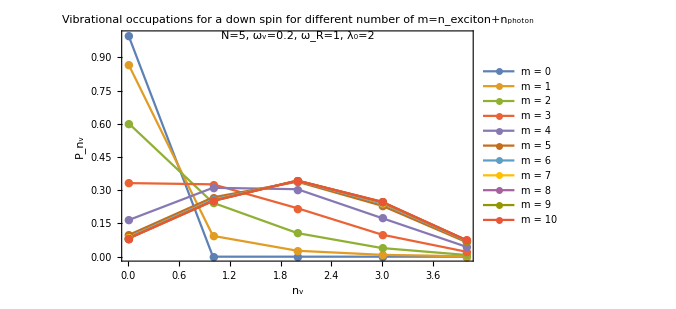

```mathematica
labels=Table["m = "<>ToString[i],{i,0,mmax}];
ListPlot[prob,Joined->True,PlotMarkers->{"●"},PlotLegends->Placed[labels,Right],PlotLabel->"Vibrational occupations for a down spin for different number of m=n_exciton+n_photon",
Epilog->Inset[Text["N="<>ToString[NN]<>", ω_v=0.2, ω_R=1, λ_0="<>ToString[lam]],{2,1}],
ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"P_n_v",None},{"n_v",None}},FrameTicks->All
]
```

```mathematica
(*prm=Max[prob[[All,2]]];
Manipulate[
ListPlot[prob[[m+1]],Joined->True,PlotMarkers->{"●"},PlotRange->{{0,M},{0,prm}}]
,{m,0,mmax,1}]*)
```

{-5.03953}

{-6.80972}

{-7.40568}

{-7.90964}

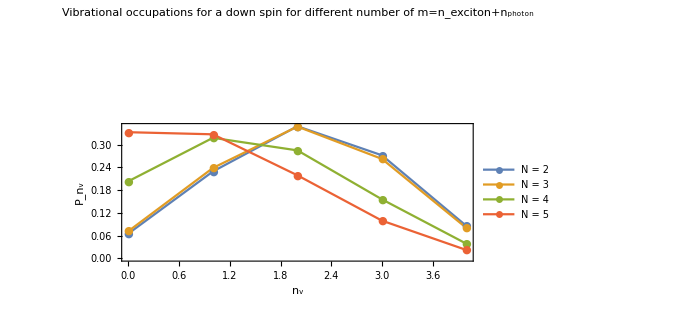

```mathematica
wv=0.2;
gg=1;
lam=2;

M=5;
Nmax=5;
m=3;

prob={};
Do[
ntot=Sum[c[NN,i],{i,0,Min[m,NN]}] * M^NN;
wvlam=wv*lam;
H = wv*makeHv[NN,M,m] + makeHg[NN,M,m,gg] + wvlam*makeHb[NN,M,m];
nn=Norm[Flatten[H]];
{eval,evec}=Eigensystem[H-nn*SparseArray[{Band[{1,1}]->1},{ntot,ntot}],1];
eval=eval+nn;eval//Print;
pr={Probvib1dn[evec[[1]]//Chop,NN,m,M]}//Transpose;
pr2=Join[{Table[i,{i,0,M-1}]}//Transpose,pr,2];
AppendTo[prob,pr2];
,{NN,2,Nmax}];

labels=Table["N = "<>ToString[i],{i,2,Nmax}];
ListPlot[prob,Joined->True,PlotMarkers->{"●"},PlotLegends->Placed[labels,Right],PlotLabel->"Vibrational occupations for a down spin for different number of m=n_exciton+n_photon",
Epilog->Inset[Text["m="<>ToString[m]<>", ω_v=0.2, ω_R=1, λ_0="<>ToString[lam]],{1,0.7}],
ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"P_n_v",None},{"n_v",None}},FrameTicks->All
]
```

```mathematica
kbT=-wv/Log[0.36]*300/0.025
```

2349.14